## PHSX 565 Astrophysical Plasma Physics Problem Set 1 - Hydrodynamics Roy Smart

### Preparing the Mathematica environment...

#### Clear Mathematica environment

```mathematica
Clear["Global`*"]
```

#### Declare Assumptions

```mathematica
$Assumptions = t >0 && r > 0 && R > 0  && ω > 0 && ρ0 > 0 &&τ >0;
```

#### Allocate arrays of evaluation rules

```mathematica
cVal = {};
```

#### Define unit vectors

```mathematica
rh = {1,0,0};
```

### The following information is provided from the problem statement

#### The heat capacity ratio

```mathematica
AppendTo[cVal, γ->5/3];
```

#### Volumetric heating rate

```mathematica
Qdot = 0
```

0

#### Unspecified radial body force

```mathematica
f = fr[t,r] rh;
```

#### Constant flow field

```mathematica
u[t_,r_] := Piecewise[{
{-(ω r)/(ω t + 1)^2 , r<=R},
{-(ω R^3)/(r^2(ω t + 1)^2) , r>R}}]rh
```

#### Plot the flow field

```mathematica
ut0 = u[t, r][[1]] /. ω-> 1 /. t-> 0/. R -> 1;
ut1 = u[t, r][[1]] /. ω-> 1 /. t-> 1/. R -> 1;
ut2 = u[t, r][[1]] /. ω-> 1 /. t-> 2/. R -> 1;
ut∞ = Series[u[t, r][[1]] /. ω-> 1 /. R -> 1,{t,∞,1}] //Normal;
```

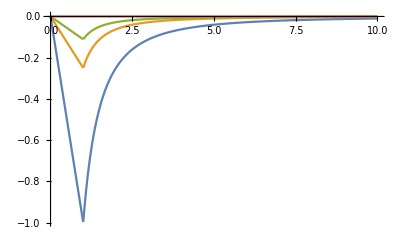

```mathematica
Plot[{ut0, ut1, ut2, ut∞},{r,0,10},PlotRange->Full]
```

### Define the advective derivative

```mathematica
DDc[f_,u_]:= D[f, t] + Dot[u,∇_{x,y,z} f]
DDs[f_,u_]:= D[f, t] + Dot[u,Grad[f,{r, θ, ϕ}, "Spherical"]]
```

### Define the fluid equations

#### Continuity equation

```mathematica
Cc[ρ_,u_ ] := D[ρ, t] + ∇_{x,y,z} .(ρ u) == 0
Cs[ρ_,u_ ] := D[ρ, t] + Div[ρ u, {r, θ, ϕ}, "Spherical"]== 0
CLs[ρ_,u_]:= DDs[ρ,u] == -ρ Div[u,{r,θ, ϕ}, "Spherical"]
```

#### Momentum equation

```mathematica
Mc[ρ_,u_,p_]:= ρ DDc[u,u] == - ∇_{x,y,z} p + f
Ms[ρ_,u_,p_]:= ρ DDs[u,u] == - Grad[p, {r,θ, ϕ}, "Spherical"]+ f
```

#### Energy equation

```mathematica
Ec[u_,p_] := DDc[p,u] == - γ p (∇_{x,y,z} .u) + (γ-1) Qdot
Es[u_,p_] := DDs[p,u] == - γ p Div[u, {r, θ, ϕ}, "Spherical"] + (γ-1) Qdot
```

## Part a.

### The density on the inner region remains uniform

```mathematica
ρc$a = D[ρ[t,r],r] ->0
```

ρ^(0,1)[t,r]→0

### The initial condition on the density is

```mathematica
ρ0$a = ρ[0,r]==ρ0;
```

### Use the Lagrangian form of the continuity equation to find the density as a function of time on the inner region

```mathematica
C0$a = CLs[ρ[t,r],Simplify[u[t,r],Assumptions->r < R]] //Simplify
```

(1+t ω)^2 ρ^(1,0)[t,r]==3 ω ρ[t,r]+r ω ρ^(0,1)[t,r]

### Apply the constraint given on the density

```mathematica
C1$a = C0$a /. ρc$a
```

(1+t ω)^2 ρ^(1,0)[t,r]==3 ω ρ[t,r]

### Solve the ODE

```mathematica
(ρ$a =DSolve[{C1$a,ρ0$a},ρ[t,r],t][[1,1]] // FullSimplify) //Framed
```

ρ[t,r]→ⅇ^((3 t ω)/(1+t ω)) ρ0

### Check that continuity equation is satisfied

```mathematica
Cs[ρ[t,r] /. ρ$a, Simplify[u[t,r],Assumptions->r < R]]  //FullSimplify
```

True

## Part b.

### We are instructed to propose a solution of the form

```mathematica
ρt$b = ρ[t,r]-> ρ0 Exp[g[t]+k[r]];
```

### Find solution that matches Part a. across the boundary r = R. (This isn’t physically necessary. Discontinuities in density are common in nature such as the surface of a body of water)

```mathematica
ρc0$b = (ρ[t,r]/.ρt$b) == (ρ[t,r]/.ρ$a) /. r-> R //Simplify
```

ⅇ^((3 t ω)/(1+t ω))==ⅇ^(g[t]+k[R])

### From the above expression we can see

```mathematica
k0$b = k[R]== 0
g$b = g[t]-> ρ$a[[2,1,2]]
```

k[R]==0

g[t]→(3 t ω)/(1+t ω)

### The derivative of g[t] is then

```mathematica
dg$b = D[g$b,t]
```

g'[t]→-(3 t ω^2)/(1+t ω)^2+(3 ω)/(1+t ω)

### Plug trial solution into the Lagrangian form of the continuity equation

```mathematica
C0$b = CLs[ρ[t,r] /. ρt$b,Simplify[u[t,r],Assumptions->r > R]] //FullSimplify
```

(r+r t ω)^2 g'[t]==R^3 ω k'[r]

### Plug in g’[t] found earlier

```mathematica
C1$b = C0$b /. dg$b
```

(r+r t ω)^2 (-(3 t ω^2)/(1+t ω)^2+(3 ω)/(1+t ω))==R^3 ω k'[r]

### Solve for k[r]

```mathematica
k$b = DSolve[{C1$b, k0$b},k[r],r][[1,1]]
```

k[r]→(r^3-R^3)/R^3

### Plug g[t] and k[r] into the proposed solution

```mathematica
(ρ$b = ρt$b /. g$b /. k$b) //Framed
```

ρ[t,r]→ⅇ^((r^3-R^3)/R^3+(3 t ω)/(1+t ω)) ρ0

### Plug into continuity equation to ensure that it is satisfied

```mathematica
Cs[ρ[t,r] /. ρ$b, Simplify[u[t,r],Assumptions->r > R]]  //FullSimplify
```

True

### Combine the answers from Part a. and b. into a single piecewise function

```mathematica
ρ$ab = Piecewise[{
{ρ[t,r] /. ρ$a, r<=R},
{ρ[t,r] /.ρ$b,  r>R}}]
```

Piecewise[{{ⅇ^((3 t ω)/(1+t ω)) ρ0, r≤R}, {ⅇ^((r^3-R^3)/R^3+(3 t ω)/(1+t ω)) ρ0, r>R}, {0, True}}]

### Sketch the density profile

#### Density profile at ωt = 0

```mathematica
ρωt0$b = ρ$ab /. (ω t) -> 0 /. (ω t) -> 0 /. R-> 1 /.ρ0 ->1
```

Piecewise[{{1, r≤1}, {ⅇ^(-1+r^3), r>1}, {0, True}}]

#### Density profile at ωt = 1

```mathematica
ρωt1$b =ρ$ab /. (ω t) -> 1 /. (ω t) -> 1 /. R-> 1/.ρ0 ->1
```

Piecewise[{{ⅇ^(3/2), r≤1}, {ⅇ^(1/2+r^3), r>1}, {0, True}}]

#### Density profile at ωt = 2

```mathematica
ρωt2$b =ρ$ab /. (ω t) -> 2 /. (ω t) -> 2 /. R-> 1/.ρ0 ->1
```

Piecewise[{{ⅇ^2, r≤1}, {ⅇ^(1+r^3), r>1}, {0, True}}]

#### Density profile as t → ∞

```mathematica
ρωt∞$b = Series[ρ$ab,{t, ∞,0}] /. R-> 1/.ρ0 ->1// Normal
```

Piecewise[{{ⅇ^3, -1+r≤0}, {ⅇ^(2+r^3), True}}]

#### Plot each evaluation

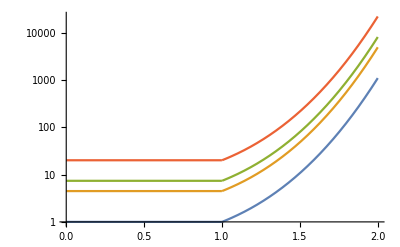

```mathematica
LogPlot[{ρωt0$b,ρωt1$b,ρωt2$b,ρωt∞$b},{r,0,2}]
```

## Part c.

### Compute the trajectory of the fluid element

#### We are given the initial condition

```mathematica
r0$c = r[τ] == R
```

r[τ]==R

#### The trajectory is found by solving the following differential equation [Longcope (1.5)]

```mathematica
t1$c = r'[t] == Simplify[u[t,r[t]][[1]],Assumptions->r[t] < R]
t2$c = r'[t] == Simplify[u[t,r[t]][[1]],Assumptions->r[t] > R]
```

r'[t]==-(ω r[t])/(1+t ω)^2

r'[t]==-(R^3 ω)/((1+t ω)^2 r[t]^2)

#### Solve for r[t] separately for each domain

```mathematica
r1$c = DSolve[{t1$c,r0$c},r[t],t][[1,1]]
r2$c = DSolve[{t2$c,r0$c},r[t],t][[1,1]]
```

r[t]→ⅇ^(1/(1+t ω)-1/(1+τ ω)) R

r[t]→(R (1-2 t ω+4 τ ω+t τ ω^2)^(1/3))/((1+t ω) (1+τ ω))^(1/3)

#### Combine back into a piecewise function

```mathematica
r$c = Piecewise[{
{r[t] /. r1$c, t < τ},
{r[t] /. r2$c, t > τ}}];
```

### Plot the trajectory

#### Evaluate the result at ωτ = 0

```mathematica
rωτ0$c = r$c /. R-> 1 /. ω-> 1 /. τ-> 0
```

Piecewise[{{ⅇ^(-1+1/(1+t)), t<0}, {(1-2 t)^(1/3)/(1+t)^(1/3), t>0}, {0, True}}]

#### Evaluate the result at ωτ = 1

```mathematica
rωτ1$c = r$c /. R-> 1 /. ω-> 1 /. τ-> 1
```

Piecewise[{{ⅇ^(-1/2+1/(1+t)), t<1}, {(5-t)^(1/3)/(2^(1/3) (1+t)^(1/3)), t>1}, {0, True}}]

#### Evaluate the result at ωτ = 2

```mathematica
rωτ2$c = r$c /. R-> 1 /. ω-> 1 /. τ-> 2
```

Piecewise[{{ⅇ^(-1/3+1/(1+t)), t<2}, {3^(1/3)/(1+t)^(1/3), t>2}, {0, True}}]

#### Evaluate the result at ωτ = ∞

```mathematica
rωτ∞$c = Series[Simplify[r$c,Assumptions->t<τ] /. R-> 1 /. ω-> 1,{τ,∞,0}] //Normal
```

ⅇ^(1/(1+t))

#### Construct the plot

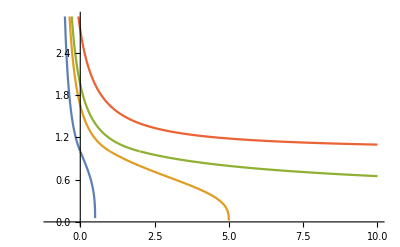

```mathematica
Plot[{rωτ0$c,rωτ1$c,rωτ2$c,rωτ∞$c},{t,-1,10}]
```

## Part d.

### Find the density ρ_τ(t)

#### Evaluate ρ(t,r) found in Parts a. and b. at r=r(t) found in part c.

```mathematica
(ρτ$d = Piecewise[{
{ρ$ab[[1,1,1]] /. r-> r$c[[1,1,1]], t ≤ τ},
{ρ$ab[[1,2,1]] /. r-> r$c[[1,2,1]]  //Simplify, t>τ}}]) //Framed
```

Piecewise[{{ⅇ^((3 t ω)/(1+t ω)) ρ0, t≤τ}, {ⅇ^((3 τ ω)/(1+τ ω)) ρ0, t>τ}, {0, True}}]

### Plot ρ_τ(t)

#### Evaluate at the same values of τ as in Part c.

```mathematica
ρτ0$d = ρτ$d /. ρ0-> 1/. ω->1/. τ-> 0;
ρτ1$d = ρτ$d  /. ρ0-> 1/. ω->1/. τ-> 1;
ρτ2$d = ρτ$d  /. ρ0-> 1/. ω->1/. τ-> 2;
ρτ∞$d = Series[Simplify[ρτ$d, Assumptions->t<τ]  /. ρ0-> 1/. ω->1,{τ,∞,0}];
```

#### Plot results

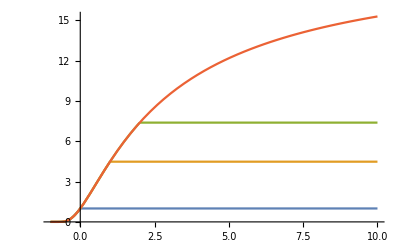

```mathematica
Plot[{ρτ0$d,ρτ1$d,ρτ2$d,ρτ∞$d},{t,-1,10}]
```

## Part e.

### Take the time derivative of ρ_τ(t) from Part d.

```mathematica
DDρτ$e=D[ρτ$d, t] //Simplify
```

Piecewise[{{(3 ⅇ^((3 t ω)/(1+t ω)) ρ0 ω)/(1+t ω)^2, t≤τ}, {0, True}}]

#### The density is constant for t > τ. Not sure what the distinction between constant and uniform is.

### Compare the results to the advective derivative of the density function found in Parts a. and b.

#### Compute the advective derivative of the result found in a. and b.

```mathematica
DDρ$e = ((DDs[ρ$ab,u[t,r]] //FullSimplify) /.(r≤ R)-> (t≤τ)) //FullSimplify
```

Piecewise[{{(3 ⅇ^((3 t ω)/(1+t ω)) ρ0 ω)/(1+t ω)^2, t≤τ}, {0, True}}]

#### Compare the two results

```mathematica
DDρτ$e == DDρ$e //FullSimplify
```

True